In this notebook, I test a single configuration with the revised version of getSigmaXY(). I have also output the derivatives for the each individual cells. The neighbor list is also recorded for the original CPU version (without any offset in the indexing). You can see that the first derivatives are now inconsistent with the Mathematica calculation, while the second derivatives are still consistent (for second derivatives, I’m using the original neighbor lists). The original neighbor list is also consistent with Mathematica.

## Analytical functions

```mathematica
(*Cross product for 2d vectors*)
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
(*The vertex position given the three adjecent cell positions*)
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
(*calculate perimetes and areas given the positions of all the vertices*)
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidgdgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*This gives the neighbor list of cell i in a counterclock-wise order and this neighbor list aligns with the vertex id list*)
```

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)];
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,voronoiPolygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
];
```

```mathematica
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
AnalyticalCell[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

```mathematica
AnalyticalCellTest[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

## Numerical function:

```mathematica
(*This function returns dei/dg and d2ei/dg^2 for each cell*)
```

```mathematica
numdericalCell[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1,ddx},{0,1}};
strainback={{1,-ddx},{0,1}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

## One snapshot with 3 false Tessellations

```mathematica
data=Import["/home/chengling/Research/Project/Cell/AnalyticalG/data/N100/derivativeTest/CPUtest_N100_p3.800_T0.10000000_999.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/d2Eidgammadgamma→NumericArray[…],/meanQ→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{10,1}],/neighbor→NumericArray[…],/overlap→NumericArray[…],/position→NumericArray[…],/sigma→NumericArray[…],/sigmai→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
(*dei/dgamma*)
```

```mathematica
Normal[data[[10,1]][[1;;100]]]
```

{3.30037,-1.2545,0.428675,8.15143,0.0936675,7.68324,11.0956,-6.80983,0.127288,0.124613,-1.18422,3.0861,2.57668,0.703032,1.94656,1.88994,4.79198,0.695642,-0.503739,5.79334,-0.967168,6.94804,-2.13489,7.46498,-0.548058,-4.66644,-2.39915,2.59506,-6.57225,6.50565,5.57891,4.73243,-3.18706,-1.04588,4.53196,2.91604,-0.442001,3.45933,-2.56281,5.70556,-1.91931,7.07167,0.105065,-6.41697,-2.56274,7.05521,1.76567,-4.20193,-1.15408,-1.42723,0.14197,1.06446,1.88517,-4.50244,2.83601,1.96624,-4.01886,-0.54224,1.78991,3.60082,1.77504,9.17145,-5.12149,0.568147,1.31687,0.099759,-2.2076,-1.18452,3.35022,-4.97627,5.48799,0.0519168,9.54036,0.303526,-0.0380749,0.256,11.5153,0.165671,-2.36584,-5.00291,-5.91042,-2.95645,-1.54567,2.08519,-3.74127,-0.438251,-1.4802,0.171802,-3.35881,-0.575386,-1.35259,1.29059,-1.29628,2.71197,-0.122034,10.177,-0.912944,3.16325,-2.56265,11.4618}

```mathematica
(*d2Edgammadgamma is d2ei/dgamma^2*)
```

```mathematica
Normal[data[[4,1]][[1;;100]]]
```

{7.14742,-1.19738,2.50265,3.41107,0.975004,6.94022,-0.380176,-6.84932,-1.56584,0.312063,-2.98919,2.93123,1.46038,0.325811,6.49752,6.07721,4.38627,7.54986,0.63955,4.57102,0.78859,1.73996,-0.125462,5.32066,0.107842,-3.62364,-4.55942,3.82895,-9.95982,6.46022,-5.07293,5.8091,-2.31085,-0.19227,4.62039,3.83586,3.04892,1.9115,-6.50125,7.17269,-3.076,0.170071,-0.687334,-4.64724,-2.03973,-1.55854,1.06885,-1.7721,-0.392947,0.602729,1.76958,2.53082,4.15476,-3.09629,3.4801,0.915507,-5.94717,-0.173985,6.3449,12.0616,0.841467,4.09071,-3.0001,4.86072,2.51749,0.829265,-5.99891,-0.235635,4.04916,-7.17523,4.20149,0.235642,30.0425,-2.63314,0.407892,9.30428,3.39004,0.311582,-0.667851,-3.78161,-4.14533,-1.37013,-0.103783,4.75635,-1.74561,0.185759,-2.30609,0.409501,-3.42784,-0.952572,-0.1787,0.870878,1.65871,2.39025,7.98105,11.8864,-0.251016,4.34019,-0.443791,34.8079}

```mathematica
positions=Table[{data[[8,1]][[2*i+1]],data[[8,1]][[2*i+2]]},{i,0,99}];
```

```mathematica
(*num is a table of {dEidgamma,d2Eidgammadgamma} for each cell calculated by numreical derivative with dgamma=0.0001*)
```

```mathematica
num=numdericalCell[positions,{10,10},0.0001,1,1,1,3.80];
```

```mathematica
stresses=Table[num[[i,1]],{i,Length[num]}]
```

{0.425409,0.640805,-0.260739,-1.72694,0.0170335,-0.0677552,0.599086,3.79861,0.215208,-0.331212,-0.0226115,-0.508655,-2.31751,-0.243869,-0.18033,-0.888692,-0.0733774,0.334739,-0.20066,-2.46604,-0.399158,1.0778,0.78108,-0.302993,-0.0696148,-0.663943,0.626654,-0.959151,-0.192916,-0.795622,0.476607,1.56762,-0.618275,-0.454452,-1.20271,-0.932501,0.364823,0.0355097,0.604879,-1.62819,-0.248258,1.77325,-0.781028,-0.562836,0.507174,2.25343,0.214664,-0.152282,-0.0815766,-0.407041,0.0329971,0.201555,-1.82997,-0.679401,0.59589,0.217055,3.15134,-0.167571,0.452144,2.0611,0.3317,0.795671,-0.248704,0.647967,-0.140904,0.0233288,3.24487,-0.0925363,-0.581975,0.307276,0.287698,0.00658032,-8.90219,1.96485,0.0874547,0.498058,-0.649639,0.051022,0.981208,-0.0465763,0.437358,-0.386442,-0.258959,-0.811029,-0.0389372,0.369949,0.0422978,0.138613,-1.04815,-0.244237,-0.469188,-0.582716,0.550521,0.0779844,0.0671172,4.71168,0.607354,0.329024,-0.439213,-7.83937}

```mathematica
d2e=Table[num[[i,2]],{i,Length[num]}]
```

{7.14742,-1.19738,2.50265,3.41107,0.975004,6.94022,-0.380175,-6.84931,-1.56584,0.312064,-2.98919,2.93124,1.46039,0.32581,6.49752,6.07721,4.38626,7.54986,0.63955,4.57102,0.78859,1.73996,-0.125462,5.32065,0.107842,-3.62355,-4.55942,3.82895,-9.95982,6.46022,-5.07293,5.8091,-2.31085,-0.192271,4.62039,3.83586,3.04892,1.91149,-6.50125,7.17269,-3.076,0.17007,-0.687385,-4.64724,-2.03973,-1.55855,1.06885,-1.7721,-0.392946,0.602729,1.76958,2.53082,4.15476,-3.09629,3.48009,0.915507,-5.94717,-0.173985,6.3449,12.0616,0.841467,4.09071,-3.0001,4.86072,2.51749,0.829264,-5.99891,-0.235636,4.04916,-7.17523,4.20148,0.235642,30.0425,-2.63314,0.407892,9.30428,3.39005,0.311582,-0.66785,-3.78161,-4.14533,-1.37013,-0.103782,4.75635,-1.74561,0.185759,-2.30609,0.4095,-3.42784,-0.952573,-0.178699,0.870878,1.65871,2.39025,7.98106,11.8864,-0.251016,4.34019,-0.443791,34.8079}

```mathematica
(*ana is a table of {dEidgamma,d2Eidgammadgamma} for each cell calculated by analytical derivative in mathematica*)
```

```mathematica
ana=AnalyticalCell[positions,{10,10},Table[i,{i,100}],1,1,1,3.80];
```

```mathematica
stressesAna=Table[ana[[i,1]],{i,Length[ana]}]
```

{0.425409,0.640805,-0.260739,-1.72694,0.0170335,-0.0677552,0.599086,3.79861,0.215208,-0.331212,-0.0226115,-0.508655,-2.31751,-0.243869,-0.18033,-0.888692,-0.0733774,0.334739,-0.20066,-2.46604,-0.399158,1.0778,0.78108,-0.302993,-0.0696148,-0.663943,0.626654,-0.959151,-0.192916,-0.795622,0.476607,1.56762,-0.618275,-0.454452,-1.20271,-0.932501,0.364823,0.0355097,0.604879,-1.62819,-0.248258,1.77325,-0.781028,-0.562836,0.507174,2.25343,0.214664,-0.152282,-0.0815765,-0.407041,0.0329971,0.201555,-1.82997,-0.679401,0.59589,0.217055,3.15134,-0.167571,0.452144,2.0611,0.3317,0.795671,-0.248704,0.647967,-0.140904,0.0233288,3.24487,-0.0925363,-0.581975,0.307276,0.287698,0.00658031,-8.90219,1.96485,0.0874547,0.498058,-0.649639,0.051022,0.981208,-0.0465763,0.437358,-0.386442,-0.258959,-0.811029,-0.0389372,0.369949,0.0422978,0.138613,-1.04815,-0.244237,-0.469188,-0.582716,0.550521,0.0779844,0.0671173,4.71168,0.607355,0.329024,-0.439213,-7.83937}

```mathematica
insGAna=Table[ana[[i,2]],{i,Length[ana]}]
```

{7.14742,-1.19738,2.50265,3.41107,0.975004,6.94022,-0.380176,-6.84932,-1.56584,0.312063,-2.98919,2.93123,1.46038,0.325811,6.49752,6.07721,4.38627,7.54986,0.63955,4.57102,0.78859,1.73996,-0.125462,5.32066,0.107842,-3.62364,-4.55942,3.82895,-9.95982,6.46022,-5.07293,5.8091,-2.31085,-0.19227,4.62039,3.83586,3.04892,1.9115,-6.50125,7.17269,-3.076,0.170071,-0.687334,-4.64724,-2.03973,-1.55854,1.06885,-1.7721,-0.392947,0.602729,1.76958,2.53082,4.15476,-3.09629,3.4801,0.915507,-5.94717,-0.173985,6.3449,12.0616,0.841467,4.09071,-3.0001,4.86072,2.51749,0.829265,-5.99891,-0.235635,4.04916,-7.17523,4.20149,0.235642,30.0425,-2.63314,0.407892,9.30428,3.39004,0.311582,-0.667851,-3.78161,-4.14533,-1.37013,-0.103783,4.75635,-1.74561,0.185759,-2.30609,0.409501,-3.42784,-0.952572,-0.1787,0.870878,1.65871,2.39025,7.98105,11.8864,-0.251016,4.34019,-0.443791,34.8079}

```mathematica
(*ana and num are consistent with each other.*)
```

```mathematica
(*the first derivatives are now inconsistent with the Mathematica calculation,while the second derivatives are still consistent*)
```

```mathematica
diffFirstD=Table[ana[[i,1]],{i,100}]-Normal[Flatten[data[[10]]]][[1;;100]]
```

{-2.87497,1.8953,-0.689414,-9.87837,-0.076634,-7.751,-10.4965,10.6084,0.0879201,-0.455825,1.16161,-3.59475,-4.89419,-0.9469,-2.12689,-2.77863,-4.86536,-0.360903,0.303079,-8.25938,0.56801,-5.87025,2.91597,-7.76798,0.478443,4.00249,3.0258,-3.55421,6.37934,-7.30127,-5.1023,-3.16481,2.56879,0.591425,-5.73467,-3.84854,0.806824,-3.42382,3.16769,-7.33375,1.67105,-5.29842,-0.886093,5.85413,3.06991,-4.80178,-1.551,4.04965,1.0725,1.02019,-0.108973,-0.8629,-3.71515,3.82304,-2.24012,-1.74918,7.1702,0.37467,-1.33777,-1.53971,-1.44334,-8.37578,4.87279,0.0798203,-1.45777,-0.0764302,5.45247,1.09198,-3.9322,5.28354,-5.20029,-0.0453365,-18.4425,1.66133,0.12553,0.242057,-12.1649,-0.114649,3.34705,4.95634,6.34778,2.57001,1.28671,-2.89622,3.70233,0.808199,1.5225,-0.0331888,2.31066,0.331149,0.883397,-1.8733,1.8468,-2.63398,0.189151,-5.46528,1.5203,-2.83422,2.12344,-19.3011}

```mathematica
diffSeconD=Table[ana[[i,2]],{i,100}]-Normal[Flatten[data[[4]]]][[1;;100]]
```

{-2.75335×10^-14,-1.00142×10^-13,-1.01252×10^-13,-5.78204×10^-13,3.75033×10^-13,1.80371×10^-11,1.01696×10^-13,-2.86704×10^-12,2.56239×10^-13,6.08624×10^-13,-4.79616×10^-14,-1.2581×10^-11,3.77476×10^-15,5.02542×10^-13,-1.33227×10^-14,3.28626×10^-14,-2.05169×10^-13,1.5099×10^-14,-1.35447×10^-14,2.1938×10^-13,-1.56763×10^-13,5.973×10^-14,2.04725×10^-13,4.44089×10^-14,-1.05332×10^-13,-6.00986×10^-12,8.52651×10^-14,-5.77316×10^-14,2.78×10^-12,-2.20268×10^-12,8.88178×10^-13,8.22453×10^-13,6.01519×10^-12,-5.94191×10^-13,1.77636×10^-14,8.12683×10^-14,7.26974×10^-13,5.39568×10^-13,1.29674×10^-13,-3.85469×10^-13,1.61116×10^-12,-1.67588×10^-13,-4.37472×10^-12,-9.25482×10^-13,-1.39444×10^-12,3.26406×10^-13,-2.84217×10^-14,2.09011×10^-12,1.67977×10^-13,4.09672×10^-14,-8.63754×10^-14,8.26006×10^-14,9.17488×10^-13,2.1827×10^-12,1.93179×10^-12,-9.10383×10^-14,-3.73479×10^-11,5.01821×10^-14,-1.81188×10^-12,2.36255×10^-13,-3.83127×10^-12,2.06057×10^-13,9.68114×10^-14,-1.55431×10^-13,-9.72555×10^-14,1.38556×10^-13,6.54943×10^-12,-4.57023×10^-13,-7.01661×10^-14,9.41469×10^-14,1.34115×10^-13,-1.45439×10^-14,-3.97904×10^-13,-3.4639×10^-13,-1.77636×10^-15,-2.04459×10^-12,-8.61533×10^-14,-4.43034×10^-13,-6.07736×10^-13,-5.62363×10^-11,8.55227×10^-12,9.04432×10^-12,4.34541×10^-13,-2.66454×10^-15,-1.26974×10^-11,9.68114×10^-14,-1.27898×10^-13,1.19127×10^-13,-7.75824×10^-13,1.54876×10^-13,1.08802×10^-14,-5.80647×10^-14,-1.66978×10^-13,-1.77636×10^-13,-3.82272×10^-12,-4.60076×10^-13,-4.57412×10^-14,2.30926×10^-13,1.10356×10^-13,1.09424×10^-12}

```mathematica
(*Let's compare the neighbor list in orginal cellGPU with Mathematica*)
```

```mathematica
box={10,10};
copies=Table[positions,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
dt=DelaunayMesh[allPointsPBD];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
```

```mathematica
dl=ListPlot[Table[{allPointsPBD[[i]]},{i,1,100}],PlotMarkers->Table[i,{i,1,100}]];
dl1=ListPlot[{allPointsPBD[[1]]},PlotMarkers->{"OpenMarkers",Large}];
```

```mathematica
allPointsPBD[[1]]
```

{4.90999,2.04256}

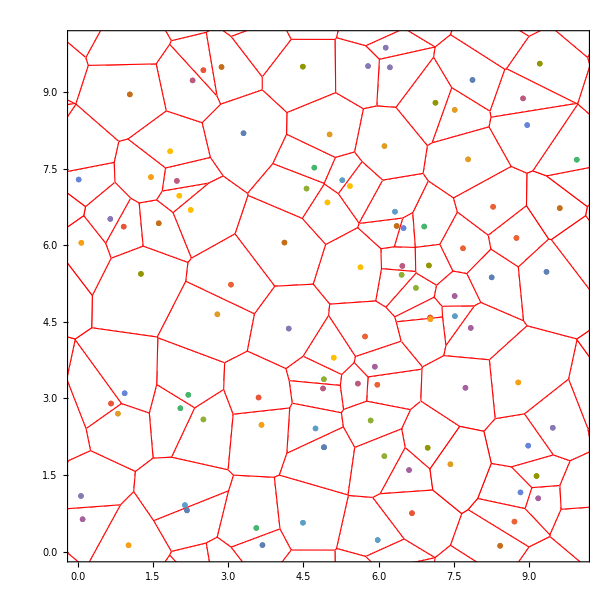

```mathematica
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red]}],dl1,dl,PlotRange->{{0,10},{0,10}},Frame->True]
```

```mathematica
(*The neighbor of cell 1 from the original cellGPU code is the same as Mathematica*)
```

```mathematica
Normal[data[[6,1]]][[1;;9]]+1
```

{93,97,28,22,3,0,0,0,0}